```mathematica
(*_______________TEST 1___VARIANT 6____________*)
```

```mathematica
(*  ___№1___ *)
Det[{{3,6,1,0},{-2,-7,-1,0},{0,0,-7,-2},{2,2,1,9}}]
```

557

```mathematica
(*____№2____*)
NullSpace[{{91,0,5,37},{2,3,7,8},{1,−3,2,1},{15,4,−4,56}}]//Length
```

0

```mathematica
(*____№3____*)
M={{1,7,2},{3,87,4},{5,9,236}};
Eigenvalues[M]//N
Inverse[M]//MatrixForm
```

{236.289,86.9875,0.723161}

(1281/929 | -817/7432 | -73/7432
-43/929 | 113/7432 | 1/7432
-51/1858 | 13/7432 | 33/7432)

```mathematica
(*____№4____*)
f[x_]:=Exp[√x]*Cos[3*x]
D[f[x],{x,5}]//FullSimplify
```

```mathematica
(ⅇ^(√x) ((105-105 √x+45 x-10 x^(3/2)-1079 x^2+1080 x^(5/2)-360 x^3+6480 x^4) Cos[3 x]-6 x (-75+√x (75-30 √x+5 x+360 x^(3/2)-360 x^2+1296 x^3)) Sin[3 x]))/(32 x^(9/2))
```

```mathematica
(*___№5___*)
NIntegrate[Cos[x^2+x+32]*Cos[Sqrt[3*x]],{x,4,6}]
```

```mathematica
0.1392030683744167
```

```mathematica
(*____№6____*)
DSolve[y''[x]+5y'[x]-15==Sin[x]+2Cos[-3x],y[x],x]
```

{{y[x]→3 x-1/5 ⅇ^(-5 x) C[1]+C[2]-(5 Cos[x])/26-1/17 Cos[3 x]-Sin[x]/26+5/51 Sin[3 x]}}

```mathematica
(*_______________TEST 2________________*)
(*________________Variant_1____________*)
```

```mathematica
(*_____________№1_______________*)
ContourPlot3D[Abs[x]+Abs[y]+Abs[z]==1,{x,-1,1},{y,-1,1},{z,-1,1},Axes->False,Boxed->False]
```

-Graphics3D-

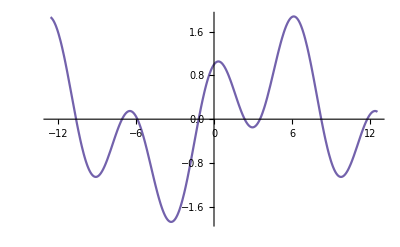

```mathematica
(*______________№2_______________*)
f[t_]:=Cos[t]+Sin[t/3]
Curve[t_]:=Abs[f''[t]]/((1+(f'[t])^2)^(3/2))
(*Plot[Curve[x],{x,-4*Pi,4*Pi}]*)
Plot[f[x],{x,-4π,4π},ColorFunction->Function[{x,y},Hue[Curve[x]/1.2]],ColorFunctionScaling->False]
```

```mathematica
(*_________________№3__________________*)
a = 1;
PseudoSphere[u_,v_]:={a*Sin[u]*Cos[v],a*Sin[u]*Sin[v],a*(Log[Tan[u/2]]+Cos[u])}
ParametricPlot3D[PseudoSphere[u,v],{u,-1,1},{v,0,2*π},MeshFunctions->{#3&},Mesh->40,ColorFunction->Function[{x,y,z},Hue[2*z]],ColorFunctionScaling->True,Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
(*_______№4________*)
Manipulate[
res = NDSolve[{y'[x] == a*y[x]*Cos[x+y[x]],y[0]==1},y,{x,-100,100}];
Plot[{Evaluate[y[x]/.res]},{x,-10,10},PlotRange->5,PlotStyle->{Blue,Thick}],{{a,0},-5,5}
]
```

```mathematica
(*  №6 (а)  Доказать с помощью компьютерного эксперимента теорему Дезарга:
Пусть даны два треугольника ABC и A1B1C1 и прямые AA1, BB1 и CC1 пересекаются в точке S. Тогда если существуют точки пересечения 
P=AC∩A1C1, Q=BC∩B1C1 и R=AB∩A1B1, то они лежат на одной прямой.

Требования: Вершины треугольника задаются с помощью Locator. *)

Letters = {"A","B","C","A1","B1","C1","R","Q","P"};
lines=Range[9];
r=Range[6];
Manipulate [ 
Show[
	Graphics[ {
	Purple,Triangle[{Pts⟦1⟧,Pts⟦2⟧,Pts⟦3⟧}],
	Yellow,Triangle[{Pts⟦4⟧,Pts⟦5⟧,Pts⟦6⟧}] }],
	Table[{
	  Graphics[ {
	  Thickness[0.001],Blue,lines⟦i⟧=InfiniteLine[{Pts⟦i⟧,Pts⟦Mod[i+1,3,1]⟧}],
	  Orange,lines⟦i+3⟧=InfiniteLine[{Pts⟦i+3⟧,Pts⟦Mod[i+1,3,1]+3⟧}],
	  Green,Thickness[0.003],Dashed,lines⟦i+6⟧=InfiniteLine[{Pts⟦i⟧,Pts⟦i+3⟧}] }]     },{i,3}] ,
Table[{
	Graphics[ {
	r⟦i⟧ ={x,y}/. Solve[{x,y}∈ lines⟦i⟧&&{x,y}∈ lines⟦i+3⟧]⟦1⟧;
	r⟦i+3⟧={x,y}/.Solve[{x,y}∈lines⟦i+6⟧&&{x,y}∈lines⟦Mod[i+1,3,1]+6⟧]⟦1⟧;

	Black,Dashing->False,Thick, InfiniteLine[{r⟦i⟧,r⟦Mod[i+1,3,1]⟧}],
	PointSize[0.017],Purple,Point[Pts⟦i⟧],
	Yellow,Point[Pts⟦i+3⟧], Red,Point[r⟦i⟧],Black,Point[r⟦i+3⟧],

	Text[Letters⟦i⟧,Pts⟦i⟧-{0.3,0.3}],
	Text[Letters⟦i+3⟧,Pts⟦i+3⟧-{0.3,0.3}],
	Text[Letters⟦i+6⟧,r⟦i⟧+{0.2,0.2}]
	}]},{i,3}],
PlotRange->{{-10,10},{-10,10}},Background->LightGreen,ImageSize->750],
{{Pts,{{-1.22,-1.57},{-3.90,-0.84},{-1,-0.27},{3,0},{0.01,4.76},{1,1}}},Locator}]
```

```mathematica
Letters = {"A","B","C","A1","B1","C1","R","Q","P"};
lines=Range[9];
r=Range[6];
Manipulate [ Pts = Insert[Pts1,c1pt,idx];(*Pts⟦6⟧=Pts⟦idx⟧; Pts⟦idx⟧ = c1pt;*)
Show[
	Graphics[ {
	Purple,Triangle[{Pts⟦1⟧,Pts⟦2⟧,Pts⟦3⟧}],
	Yellow,Triangle[{Pts⟦4⟧,Pts⟦5⟧,Pts⟦6⟧}] }],
	Table[{
	  Graphics[ {
	  Thickness[0.001],Blue,lines⟦i⟧=InfiniteLine[{Pts⟦i⟧,Pts⟦Mod[i+1,3,1]⟧}],
	  Orange,lines⟦i+3⟧=InfiniteLine[{Pts⟦i+3⟧,Pts⟦Mod[i+1,3,1]+3⟧}],
	  color,Thickness[0.003],Dashed,lines⟦i+6⟧=InfiniteLine[{Pts⟦i⟧,Pts⟦i+3⟧}] }]     },{i,3}] ,
Table[{
	Graphics[ {
	r⟦i⟧ ={x,y}/. Solve[{x,y}∈ lines⟦i⟧&&{x,y}∈ lines⟦i+3⟧]⟦1⟧;
	r⟦i+3⟧={x,y}/.Solve[{x,y}∈lines⟦i+6⟧&&{x,y}∈lines⟦Mod[i+1,3,1]+6⟧]⟦1⟧;

	Black,Dashing->False,Thick, InfiniteLine[{r⟦i⟧,r⟦Mod[i+1,3,1]⟧}],
	PointSize[0.017],Purple,Point[Pts⟦i⟧],
	Yellow,Point[Pts⟦i+3⟧], Red,Point[r⟦i⟧],Black,Point[r⟦i+3⟧],

	Text[Letters⟦i⟧,Pts⟦i⟧-{0.3,0.3}],
	Text[Letters⟦i+3⟧,Pts⟦i+3⟧-{0.3,0.3}],
	Text[Letters⟦i+6⟧,r⟦i⟧+{0.2,0.2}]
	}]},{i,3}],
PlotRange->{{-10,10},{-10,10}},Background->LightGreen,ImageSize->550],
{{Pts1,{{-1.22,-1.57},{-3.90,-0.84},{-1,-0.27},{3,0},{0.01,4.76}}},Locator},
{{idx,6,"Point"},{1,2,3,4,5,6}},
{{c1pt,{1,1}},{-2,-2},{2,2}},
{color,Green}]
```